```mathematica
(* III. continuous gw *)
```

```mathematica
n=3;ep=LeviCivitaTensor[3,List];alcoord={al,be,ga};alcoordd={aldot,bedot,gadot};phcoord={phx,phy,phz};phcoordd={phxdot,phydot,phzdot};phpcoord={phpx,phpy,phpz};phpcoordd={phpxdot,phpydot,phpzdot};gap={gapx,gapy,gapz};reuler={{Cos[al] Cos[ga]-Cos[be] Sin[al] Sin[ga],Cos[ga] Sin[al]+Cos[al] Cos[be] Sin[ga],Sin[be] Sin[ga]},{-Cos[be] Cos[ga] Sin[al]-Cos[al] Sin[ga],Cos[al] Cos[be] Cos[ga]-Sin[al] Sin[ga],Cos[ga] Sin[be]},{Sin[al] Sin[be],-Cos[al] Sin[be],Cos[be]}};inversereuler=Simplify[Inverse[reuler]];MatrixForm[inversereuler]
```

(Cos[al] Cos[ga]-Cos[be] Sin[al] Sin[ga] | -Cos[be] Cos[ga] Sin[al]-Cos[al] Sin[ga] | Sin[al] Sin[be]
Cos[ga] Sin[al]+Cos[al] Cos[be] Sin[ga] | Cos[al] Cos[be] Cos[ga]-Sin[al] Sin[ga] | -Cos[al] Sin[be]
Sin[be] Sin[ga] | Cos[ga] Sin[be] | Cos[be])

```mathematica
(* angular velocity *)
```

```mathematica
tranalphp={{Sin[be]*Sin[ga],Cos[ga],0},{Sin[be]*Cos[ga],-Sin[ga],0},{Cos[be],0,1}};inversetranalphp=Simplify[Inverse[tranalphp]];omp=tranalphp.alcoordd;omi=Simplify[inversereuler.omp,Assumptions->{al∈Reals,be∈Reals,ga∈Reals}];ompf=omp/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};omif=omi/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};xpaxis={Cos[al]*Cos[ga]-Sin[al]*Cos[be]*Sin[ga],Sin[al]*Cos[ga]+Cos[al]*Cos[be]*Sin[ga],Sin[be]*Sin[ga]};ypaxis={-Cos[al]*Sin[ga]-Sin[al]*Cos[be]*Cos[ga],-Sin[al]*Sin[ga]+Cos[al]*Cos[be]*Cos[ga],Sin[be]*Cos[ga]};zpaxis={Sin[be]*Sin[al],-Sin[be]*Cos[al],Cos[be]};xpaxisf=xpaxis/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};ypaxisf=ypaxis/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};zpaxisf=zpaxis/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};
```

```mathematica
(* kinetic energy *)
```

```mathematica
ip={{ipxx,0,0},{0,ipyy,0},{0,0,ipzz}};tp=Simplify[1/2*Sum[ip[[i,j]]*omp[[i]]*omp[[j]],{i,1,n},{j,1,n}]];
```

```mathematica
(* potential energy *)
```

```mathematica
scoeffi={{sxx,sxy,sxz},{sxy,syy,syz},{sxz,syz,szz}};scoeffp=Table[Simplify[Sum[reuler[[k,i]]*reuler[[l,j]]*scoeffi[[i,j]],{i,1,n},{j,1,n}]],{k,1,n},{l,1,n}];deeg=cc*scoeffp[[3,3]];
```

```mathematica
(* Euler equation *)
```

```mathematica
gaplv=Table[Simplify[Sum[-2*cc*scoeffi[[j,k]]*reuler[[3,k]]*inversereuler[[j,l]]*ep[[i,3,l]],{j,1,n},{k,1,n},{l,1,n}]],{i,1,n}];eueq1=Table[Simplify[D[Sum[ip[[i,j]]*ompf[[j]],{j,1,n}],t]+Sum[ip[[j,k]]*omp[[j]]*omp[[l]]*ep[[l,k,i]],{j,1,n},{k,1,n},{l,1,n}]-gaplv[[i]]/.{al->alf[t],be->bef[t],ga->gaf[t]}],{i,1,n}]/.{alf''[t]->alddot,bef''[t]->beddot,gaf''[t]->gaddot,alf'[t]->aldot,bef'[t]->bedot,gaf'[t]->gadot,alf[t]->al,bef[t]->be,gaf[t]->ga};eueq2=Table[Simplify[Sum[eueq1[[i]]*tranalphp[[i,j]],{i,1,n}]],{j,1,n}];gaallv=Table[Simplify[-D[deeg,alcoord[[i]]]],{i,1,n}];eueq4=Table[Simplify[D[D[tp,alcoordd[[i]]]/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]},t]-D[tp,alcoord[[i]]]-gaallv[[i]]/.{alf''[t]->alddot,bef''[t]->beddot,gaf''[t]->gaddot,alf'[t]->aldot,bef'[t]->bedot,gaf'[t]->gadot,alf[t]->al,bef[t]->be,gaf[t]->ga}],{i,1,n}];Simplify[eueq2-eueq4]
```

{0,0,0}

```mathematica
(* h_+, h_× *)
```

```mathematica
thhat={Cos[th]*Cos[vp],Cos[th]*Sin[vp],-Sin[th]};vphat={-Sin[vp],Cos[vp],0};c2abc={{2*(de2*(omp[[2]])^2-de3*(omp[[3]])^2),de3/ipzz*gap[[3]]+dxy*omp[[1]]*omp[[2]],de2/ipyy*gap[[2]]+dxz*omp[[1]]*omp[[3]]},{de3/ipzz*gap[[3]]+dxy*omp[[1]]*omp[[2]],2*(de3*(omp[[3]])^2-de1*(omp[[1]])^2),de1/ipxx*gap[[1]]+dyz*omp[[2]]*omp[[3]]},{de2/ipyy*gap[[2]]+dxz*omp[[1]]*omp[[3]],de1/ipxx*gap[[1]]+dyz*omp[[2]]*omp[[3]],2*(de1*(omp[[1]])^2-de2*(omp[[2]])^2)}}/.{de1->ipyy-ipzz,de2->ipzz-ipxx,de3->ipxx-ipyy,dxy->(ipxx-ipyy)^2/ipzz+ipyy-2*ipzz+ipxx,dxz->(ipzz-ipxx)^2/ipyy+ipxx-2*ipyy+ipzz,dyz->(ipyy-ipzz)^2/ipxx+ipzz-2*ipxx+ipyy};c2iabc=inversereuler.c2abc.reuler;hplus=1/2*Sum[(thhat[[i]]*thhat[[j]]-vphat[[i]]*vphat[[j]])*c2iabc[[i,j]],{i,1,n},{j,1,n}];hcross=1/2*Sum[(thhat[[i]]*vphat[[j]]+vphat[[i]]*thhat[[j]])*c2iabc[[i,j]],{i,1,n},{j,1,n}];thhatp=Simplify[reuler.thhat,Assumptions->{al∈Reals,be∈Reals,ga∈Reals,th∈Reals,vp∈Reals}];vphatp=Simplify[reuler.vphat,Assumptions->{al∈Reals,be∈Reals,ga∈Reals,,th∈Reals,vp∈Reals}];
```

```mathematica
(* numerical values *)
```

```mathematica
cc1=1;sxx1=-0.01;syy1=0.02;szz1=0.05;sxy1=0.0;sxz1=0.0;syz1=0;ipxx1=1;ipyy1=1;ipzz1=1.1;tf1=2000;numeueq=eueq4/.{cc->cc1,sxx->sxx1,syy->syy1,szz->szz1,sxy->sxy1,sxz->sxz1,syz->syz1,ipxx->ipxx1,ipyy->ipyy1,ipzz->ipzz1,al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t],alddot->alf''[t],beddot->bef''[t],gaddot->gaf''[t]};numeueq2=eueq4/.{cc->0,sxx->sxx1,syy->syy1,szz->szz1,sxy->sxy1,sxz->sxz1,syz->syz1,ipxx->ipxx1,ipyy->ipyy1,ipzz->ipzz1,al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t],alddot->alf''[t],beddot->bef''[t],gaddot->gaf''[t]};deeg1=deeg/.{cc->cc1,sxx->sxx1,syy->syy1,szz->szz1,sxy->sxy1,sxz->sxz1,syz->syz1};gaplv1=gaplv/.{cc->cc1,sxx->sxx1,syy->syy1,szz->szz1,sxy->sxy1,sxz->sxz1,syz->syz1};hplus1=hplus/.{cc->cc1,sxx->sxx1,syy->syy1,szz->szz1,sxy->sxy1,sxz->sxz1,syz->syz1,gapx->gaplv1[[1]],gapy->gaplv1[[2]],gapz->gaplv1[[2]],ipxx->ipxx1,ipyy->ipyy1,ipzz->ipzz1};hcross1=hcross/.{cc->cc1,sxx->sxx1,syy->syy1,szz->szz1,sxy->sxy1,sxz->sxz1,syz->syz1,gapx->gaplv1[[1]],gapy->gaplv1[[2]],gapz->gaplv1[[2]],ipxx->ipxx1,ipyy->ipyy1,ipzz->ipzz1};
```

```mathematica
(* solution I *)
```

```mathematica
al1=Pi/2;be1=0.697;ga1=0;aldot1=1.391;bedot1=0;gadot1=1-aldot1*Cos[be1];
```

```mathematica
(* solution II *)
```

```mathematica
solal=NDSolve[{numeueq[[1]]==0,numeueq[[2]]==0,numeueq[[3]]==0,alf[0]==al1,bef[0]==be1,gaf[0]==ga1,alf'[0]==aldot1,bef'[0]==bedot1,gaf'[0]==gadot1},{alf,bef,gaf},{t,0,tf1}]
```

{{alf→InterpolatingFunction[{{0., 2000.}}, <>],bef→InterpolatingFunction[{{0., 2000.}}, <>],gaf→InterpolatingFunction[{{0., 2000.}}, <>]}}

```mathematica
thob1=N[0.8];phob1=0;hplus11=hplus1/.{th->thob1,vp->phob1,al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};hcross11=hcross1/.{th->thob1,vp->phob1,al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};
```

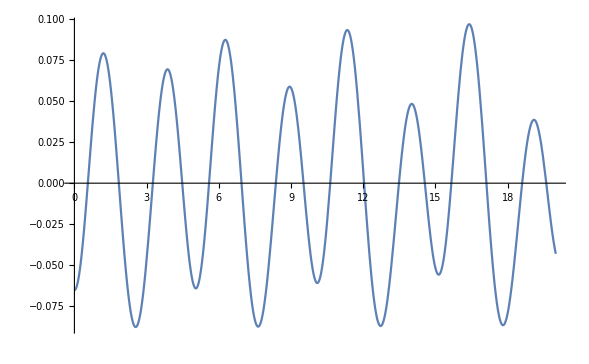

```mathematica
Plot[{Evaluate[hplus11/.solal[[1]]]},{t,0,20}]
```

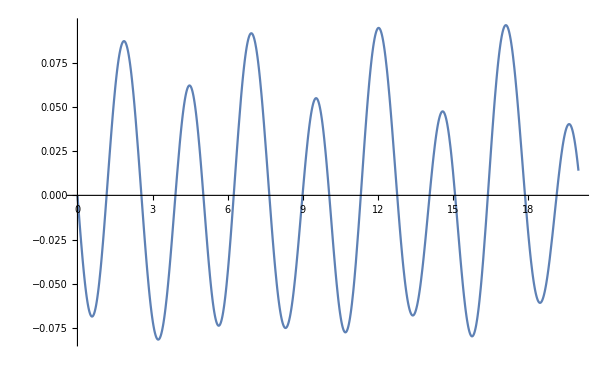

```mathematica
Plot[{Evaluate[hcross11/.solal[[1]]]},{t,0,20}]
```

```mathematica
function=Evaluate[-2*hplus11/.solal[[1]]];
y=Table[function,{t,0,tf1,0.1}];
x=Table[t,{t,0,tf1,0.1}];
F=Transpose@{x,y};
Export["desktop/lorentz_precession/data2/plus2.dat",F];
```

$Aborted[]

Part::partw: Part 2 of {{«1»}} does not exist.

$Aborted[]

ReplaceAll::reps: {{{alf→InterpolatingFunction[{{«2»}},{5,7,2,{«1»},{«1»},0,0,0,0,Automatic,{},{},False},{{«76584»}},{Developer`PackedArrayForm,{«76585»},{«229752»}},{Automatic}],bef→InterpolatingFunction[{{«2»}},{5,7,2,{«1»},{«1»},0,0,0,0,Automatic,{},{},False},{{«76584»}},{Developer`PackedArrayForm,{«76585»},{«229752»}},{Automatic}],gaf→InterpolatingFunction[{{«2»}},{5,7,2,{«1»},{«1»},0,0,0,0,Automatic,{},{},False},{{«76584»}},{Developer`PackedArrayForm,{«76585»},{«229752»}},{Automatic}]}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
function=Evaluate[-2*hcross11/.solal[[1]]];
y=Table[function,{t,0,tf1,0.1}];
x=Table[t,{t,0,tf1,0.1}];
F=Transpose@{x,y};
Export["desktop/lorentz_precession/data2/cross1.dat",F];
```